```mathematica
f1[x_]:=Piecewise[{{1300,x≥16},{355.55-227.157 x+41.8716 x^2-1.50295 x^3   ,x≥3&&x<16}},0];
f2[x_]:=Piecewise[{{-538.619+221.314 x-12.222 x^2+0.214161 x^3 ,x≥15.8},{263.514-158.78 x+27.7852 x^2-1.00023 x^3,x>3.3&&x<15.8}},0];
f3[x_]:=Piecewise[{{700,x≥15},{268.082-167.384 x+29.8417 x^2-1.12005 x^3 ,x≥4&&x<15}},0];
f8[x_]:=Piecewise[{{800,x≥11.9},{252.539-151.908 x+25.8963 x^2-0.77603 x^3    ,x≥3&&x<11.9}},0];
f4[x_]:=Piecewise[{{-494.027+181.306 x-9.3211 x^2+0.151224 x^3 ,x≥15.8},{240.569-144.836 x+24.7466 x^2-0.885927 x^3,x≥4&&x<15.8}},0];
f5[x_]:=Piecewise[{{4354.75-514.055 x+23.4929 x^2-0.366667 x^3  ,x≥21},{-5181.63+933.852 x-49.2246 x^2+0.842593 x^3,x≥16&&x<21},{120.06-86.8705 x+17.273 x^2-0.621799 x^3,x≥2.39&&x<16}},0];
f6[x_]:=Piecewise[{{-197.091+166.499 x-10.0478 x^2+0.184732 x^3  ,x>15},{287.856-167.001 x+28.1616 x^2-1.02506 x^3 ,x≥3.3&&x≤15}},0];
f7[x_]:=Piecewise[{{276.926+105.891 x-5.78896 x^2+0.10101 x^3  ,x≥16.4},{168.218-121.365 x+24.3898 x^2-0.870014 x^3 ,x≥3.3&&x<16.4}},0];
f9[x_]:=Piecewise[{{-2153.68+593.426 x-32.2453 x^2+0.546426 x^3   ,x≥15.9},{606.645-336.629 x+54.1035 x^2-1.89526 x^3  ,x≥3.5&&x<15.9}},0];
f[x_]:= f1[x]+4*f2[x]+4*f3[x]+4*f4[x]+4*f5[x]+4*f6[x]+f7[x]+f8[x]+f9[x];
Range[2,2184,1]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2168,2169,2170,2171,2172,2173,2174,2175,2176,2177,2178,2179,2180,2181,2182,2183,2184}

```mathematica
speedData = Import["D:\\Documents\\uni\\2_курс\\Моделиране\\all_data2020.xlsx",{"Data",1,Range[2,2184,1],2}]
```

{4.28,3.68,3.42,3.4,3.2,3.93,4.42,4.71,3.28,2.8,3.8,3.92,3.82,3.02,2.53,1.8,2.24,3.87,4.46,3.51,3.38,3.88,3.18,4.63,5.99,5.78,6.45,3.84,3.44,3.93,5.52,6.87,8.9,9.56,9.91,9.51,11.2,11.01,10.79,10.83,8.48,8.17,9.94,9.4,8.82,9.14,9.57,7.19,6.,5.23,4.89,5.11,5.96,5.62,4.64,3.76,3.23,2.19,1.71,2.,2.33,1.54,2.78,3.99,3.94,3.4,2.57,2.87,3.27,2.92,2.99,3.84,3.83,4.34,5.07,5.24,4.9,4.09,4.74,5.04,6.12,6.28,6.5,7.55,7.65,7.08,7.08,6.43,6.05,6.2,6.1,5.37,6.58,8.08,8.02,7.36,7.13,7.05,6.95,6.79,6.37,5.97,5.83,5.34,4.65,4.2,4.18,3.78,3.,2.88,2.61,1.24,0.96,1.66,3.11,2.67,3.33,4.03,3.28,4.25,5.48,5.14,4.25,4.7,4.89,6.,6.04,6.74,6.44,5.46,6.34,6.66,5.33,3.98,4.14,3.19,3.77,4.19,2.74,3.1,5.34,5.16,3.44,4.72,6.1,5.14,5.,4.4,4.71,4.29,4.12,4.94,4.36,3.49,3.42,3.54,2.13,1.97,2.48,2.89,3.17,3.73,4.66,4.16,3.35,4.17,4.76,3.63,3.57,3.4,2.78,2.85,3.16,4.01,3.52,2.94,3.63,4.,3.6,3.56,4.53,3.95,4.61,4.72,5.49,6.26,7.91,7.82,5.86,5.44,6.9,6.97,6.97,8.06,9.37,10.64,9.69,10.15,11.29,13.95,14.69,14.77,16.68,14.14,11.36,0.,0.,6.28,5.09,4.85,0.,0.,3.47,7.96,0.,4.75,0.,0.,0.,3.73,4.23,4.31,4.28,0.,4.59,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.04,11.18,10.3,10.99,11.46,12.38,13.51,15.68,15.53,15.65,15.25,15.22,14.88,15.06,17.01,17.26,16.11,14.34,15.52,14.15,14.36,12.96,12.76,12.97,14.29,15.44,15.31,18.58,19.72,19.31,17.26,15.07,15.57,15.71,12.46,12.32,15.02,17.91,18.44,18.46,18.41,18.33,17.71,13.57,7.46,6.62,6.09,4.58,6.21,6.7,0.,5.2,6.47,0.,0.,0.,0.,7.2,0.,0.,0.,6.57,8.41,13.29,0.,0.,11.57,0.,0.,16.52,13.83,0.,0.,15.06,0.,0.,17.46,0.,7.85,11.21,7.56,0.,10.58,0.,11.19,0.,13.01,10.12,0.,0.,0.,0.,0.,8.64,5.36,3.42,7.35,5.9,0.,7.96,6.55,7.23,4.95,4.26,4.58,4.34,4.54,5.36,5.86,4.12,6.29,7.2,7.5,8.28,9.67,9.46,9.65,10.43,8.38,7.69,15.44,14.01,11.44,11.12,7.81,7.44,7.63,5.57,7.22,4.4,7.64,7.49,8.25,7.36,7.98,8.66,8.79,11.32,8.16,6.99,6.79,9.4,10.96,12.43,13.13,14.41,14.45,13.57,13.6,14.02,13.37,11.8,10.75,12.1,14.29,15.4,16.54,16.5,16.85,16.28,17.63,15.38,14.64,15.45,15.12,15.98,14.43,16.26,15.51,15.34,17.69,17.29,17.02,16.63,16.43,15.19,11.89,9.96,9.8,14.19,12.98,14.06,13.92,11.5,12.51,12.3,11.05,12.55,10.56,13.43,15.57,14.24,12.76,12.49,12.,12.78,12.43,13.46,12.64,13.52,13.46,11.86,13.74,15.05,12.9,10.78,10.41,12.25,10.7,11.47,11.44,11.45,12.41,10.17,9.58,8.98,8.41,9.06,9.27,9.01,6.72,6.4,5.74,6.67,5.11,6.69,6.79,5.46,4.1,5.57,5.82,6.15,5.86,5.15,5.01,5.32,5.26,5.26,6.15,6.7,6.27,4.86,4.34,5.61,5.24,4.56,2.41,2.2,1.23,2.33,2.6,3.36,3.76,3.34,4.61,4.12,4.14,3.15,4.47,4.32,3.07,3.16,3.81,3.43,4.03,3.1,3.05,3.25,2.47,1.39,2.36,2.88,3.76,3.79,3.3,2.81,2.38,0.94,0.43,0.95,0.84,2.37,2.85,2.88,2.47,3.34,2.26,1.09,1.77,2.09,2.45,1.75,1.3,1.81,3.57,4.62,3.89,2.79,2.36,1.46,2.68,3.48,4.24,5.04,6.33,7.47,6.52,6.73,7.45,8.22,8.61,8.43,10.31,10.94,10.23,9.38,11.38,12.04,11.11,11.49,10.91,11.24,12.64,13.12,12.42,13.64,12.52,10.2,10.28,10.76,8.13,7.31,9.57,9.27,10.47,10.61,12.22,12.61,14.87,15.6,16.57,17.09,15.02,15.81,15.3,16.9,16.26,8.64,8.7,9.43,10.32,10.53,10.4,9.37,9.83,9.62,8.26,7.22,7.83,7.39,6.69,7.6,6.19,4.56,2.9,2.28,1.61,1.51,3.92,4.8,6.,5.92,5.6,6.46,7.64,9.12,9.56,9.93,9.05,9.7,9.02,7.46,5.61,10.17,12.58,13.73,15.65,14.9,13.88,14.42,14.76,14.95,15.14,14.14,14.23,14.63,14.72,14.65,13.43,13.71,12.24,12.16,13.36,11.54,11.78,10.03,12.12,11.18,10.31,11.68,10.85,10.52,10.53,10.1,10.89,11.42,11.06,11.33,10.79,10.23,8.56,9.33,9.64,9.6,11.09,11.4,11.03,10.2,9.67,9.93,8.19,8.09,8.61,9.28,11.17,10.99,11.4,10.82,11.95,10.34,6.91,6.95,10.85,11.64,12.06,13.72,15.22,14.93,14.94,13.26,11.45,10.47,9.91,9.11,10.24,10.84,10.56,10.49,10.96,11.85,12.79,14.9,13.43,11.83,12.08,12.16,11.74,12.61,12.41,14.21,12.59,13.73,11.77,11.34,12.22,12.53,11.92,10.77,10.59,7.5,8.43,9.73,11.78,10.31,13.32,13.54,12.7,11.82,11.12,12.13,10.42,9.76,10.94,10.47,5.53,4.2,6.21,7.12,5.54,7.23,7.14,7.46,7.84,9.8,6.98,9.04,11.18,12.47,13.04,11.46,11.88,10.05,9.44,9.36,5.76,5.13,7.47,7.07,7.04,5.52,5.39,5.76,2.54,2.71,2.49,0.99,0.86,1.28,0.97,2.27,2.35,2.65,2.77,4.02,3.99,4.9,5.8,7.48,6.7,7.36,7.91,8.01,8.92,9.32,8.63,8.5,8.46,8.11,8.17,7.97,8.12,9.09,8.61,9.11,8.26,7.32,5.94,6.37,6.27,5.99,6.02,6.13,6.49,5.59,5.63,6.24,7.15,8.08,7.07,5.18,4.76,4.07,4.39,3.58,3.49,4.31,4.38,5.94,6.1,4.64,6.18,7.2,5.97,5.15,3.93,2.79,4.66,3.91,4.86,7.61,6.16,7.62,4.77,6.74,8.4,7.82,5.77,5.61,6.68,5.52,6.59,6.66,8.23,12.43,10.81,10.6,8.85,10.35,10.53,10.22,9.02,9.99,9.39,8.17,8.8,5.85,5.22,3.94,3.87,4.9,4.26,3.56,2.64,1.3,2.43,3.95,5.31,6.87,7.05,5.76,7.09,7.16,6.44,7.3,8.17,8.66,8.83,9.97,9.09,7.87,7.94,11.39,11.07,11.54,11.12,10.,13.45,13.89,14.35,13.94,14.82,14.35,14.49,13.15,12.46,14.12,13.2,12.1,13.38,13.24,14.58,13.1,13.68,12.78,14.37,13.07,13.97,13.51,11.74,12.31,11.78,11.18,11.39,10.17,10.59,10.39,12.39,11.5,11.91,10.12,9.68,9.62,8.83,8.51,8.68,8.74,8.68,7.26,8.16,8.76,7.84,7.56,6.97,4.41,4.15,6.62,6.25,5.51,5.14,4.1,3.02,1.58,1.3,2.32,1.85,1.26,1.21,0.4,0.98,2.31,3.33,1.78,1.53,0.83,1.68,3.85,4.07,3.66,3.3,3.51,4.27,4.12,4.06,3.31,2.62,4.59,5.25,6.74,7.48,8.19,6.19,7.43,8.57,9.94,9.36,10.53,11.12,13.34,12.22,11.39,12.2,10.94,10.25,10.06,10.04,9.79,8.46,8.04,8.08,6.2,4.64,3.8,5.87,6.88,7.31,6.71,6.05,7.01,8.21,7.65,7.75,7.5,7.13,5.62,6.84,7.12,5.83,6.41,6.97,7.18,8.06,6.38,5.25,6.89,7.24,6.28,4.67,4.8,5.6,5.36,7.38,8.43,7.01,8.19,9.65,10.03,9.38,10.43,9.97,11.12,7.71,5.96,11.23,12.63,12.,13.13,14.13,13.64,12.1,12.42,14.02,15.36,12.79,14.14,14.23,15.97,17.25,14.96,15.46,15.91,16.36,17.62,19.48,20.96,21.96,20.76,19.32,20.18,18.76,17.05,15.41,15.92,16.71,15.89,17.02,15.22,14.67,9.57,6.67,3.09,7.41,7.38,7.33,6.08,8.61,7.55,5.32,4.77,5.,5.64,5.58,5.62,6.98,7.42,6.54,8.02,8.93,6.43,5.53,3.6,3.28,2.15,2.03,2.5,1.93,1.78,2.91,1.33,1.06,1.29,2.26,2.03,1.1,1.58,1.01,2.8,2.79,2.09,2.11,4.33,5.46,4.81,4.77,3.48,3.45,2.83,2.52,1.78,2.46,2.41,1.89,0.62,0.54,0.9,0.52,0.63,1.87,2.99,4.07,4.77,4.1,3.24,2.84,4.27,4.03,3.98,2.86,2.64,2.57,2.47,5.1,6.65,7.87,7.97,7.67,7.91,7.71,8.42,8.01,8.33,8.62,10.01,9.02,7.55,6.01,3.54,2.67,1.81,3.66,5.07,5.96,5.94,5.6,5.26,4.97,5.86,4.14,4.62,6.81,5.32,6.49,6.51,7.,8.17,8.1,6.84,6.43,5.84,5.43,4.34,3.72,2.76,1.51,1.48,2.85,2.04,2.82,2.84,1.87,2.88,2.74,3.78,4.15,3.96,3.53,2.86,2.37,1.3,3.27,6.7,3.32,2.44,1.69,1.75,1.87,3.22,3.47,1.95,2.84,1.8,1.82,2.,2.72,3.2,3.42,3.82,3.22,3.48,3.15,2.41,2.72,4.12,3.95,3.22,1.83,0.97,1.06,0.98,1.7,2.71,2.57,3.28,3.53,3.96,3.71,2.24,1.44,1.7,1.71,2.34,2.71,3.53,4.85,4.2,4.46,6.06,6.1,6.31,5.23,4.32,6.44,8.79,8.3,6.92,7.63,4.64,6.37,5.28,6.8,8.28,9.97,10.8,11.79,10.31,7.33,7.3,7.22,8.16,8.8,7.84,8.51,8.13,6.08,7.02,7.78,10.68,10.2,8.09,7.71,7.35,7.36,6.54,7.64,8.2,4.99,4.29,3.72,3.2,3.09,4.18,2.99,3.74,4.39,3.33,7.52,4.18,4.44,4.76,3.85,5.32,5.7,4.16,3.83,4.72,7.76,8.67,10.03,10.56,12.11,12.02,11.54,12.91,14.,13.87,13.29,14.22,13.56,11.25,9.14,9.21,9.14,7.14,7.24,9.69,9.9,9.21,6.54,3.9,3.86,3.26,7.81,8.72,8.43,8.25,9.91,9.44,9.16,9.76,9.,7.58,5.49,5.28,7.13,6.12,9.07,10.29,9.66,9.98,10.02,11.57,11.5,10.9,11.43,11.4,13.09,13.45,14.31,15.92,14.92,13.25,13.3,21.,15.13,16.46,15.5,14.8,13.5,14.3,13.21,11.06,13.7,9.43,11.99,14.54,14.5,12.01,9.88,10.01,13.1,11.84,12.72,12.46,13.31,14.4,16.89,17.32,17.34,16.83,13.33,12.82,11.27,13.21,12.77,13.74,14.28,14.28,14.19,14.29,14.72,14.,12.96,13.8,9.44,7.69,6.6,7.26,10.79,18.49,16.54,14.19,18.04,11.02,11.57,11.82,13.2,15.85,11.89,14.01,11.46,11.12,9.48,8.35,8.32,6.17,7.84,8.38,9.38,10.63,12.47,12.24,11.27,11.33,14.4,17.21,19.56,18.18,17.63,15.76,13.34,10.84,9.43,9.33,8.28,7.38,6.4,6.73,6.85,6.72,7.31,6.03,7.62,9.65,10.35,11.34,11.28,12.32,12.69,11.86,13.21,12.16,12.5,12.05,12.27,10.89,10.18,10.03,9.68,11.59,11.78,11.56,11.11,12.53,12.68,13.98,15.82,15.62,17.76,17.83,18.24,17.67,15.26,11.64,11.97,14.15,13.49,13.03,12.56,14.28,13.24,13.59,12.32,12.56,11.88,11.52,8.54,6.02,5.65,8.,9.44,13.49,10.2,10.85,14.35,13.98,13.14,13.77,11.96,14.92,15.87,13.2,13.29,12.99,11.98,10.53,12.67,12.44,13.61,12.65,12.2,9.8,7.93,7.88,7.08,8.07,8.16,7.82,6.9,7.16,6.7,6.86,6.63,5.51,3.19,3.73,4.01,3.25,2.28,2.55,4.06,4.,4.44,5.87,6.36,6.7,5.74,6.44,7.2,7.48,7.46,9.16,9.45,8.87,10.92,8.04,8.76,9.87,8.98,8.45,8.16,8.29,8.58,9.03,9.72,9.5,10.67,7.86,9.18,7.73,6.56,5.63,6.1,5.76,5.16,5.93,4.65,5.5,2.67,2.86,2.43,2.36,2.38,2.69,4.47,3.61,4.51,4.94,5.07,4.84,4.66,5.06,3.91,3.27,2.67,2.1,1.86,3.59,4.4,6.47,6.52,7.66,7.5,6.24,6.15,5.08,5.69,5.83,6.13,6.76,5.76,5.74,4.93,6.56,6.11,5.46,5.09,6.09,5.91,5.85,4.39,6.41,6.11,5.98,5.86,4.94,3.69,3.25,2.68,2.56,1.69,1.84,1.52,2.95,2.12,1.42,3.33,4.89,3.76,3.95,4.2,5.76,5.34,6.9,5.55,5.92,5.09,3.,2.25,2.34,3.75,3.59,2.58,2.72,1.97,3.04,3.64,3.84,2.99,4.12,4.7,4.97,6.06,6.74,7.47,7.79,6.54,5.52,6.25,6.68,7.43,7.98,7.99,7.71,7.22,7.27,6.52,6.33,6.77,5.99,6.37,5.82,6.16,6.21,5.95,4.43,4.88,4.27,4.83,3.,3.44,2.97,3.56,3.48,3.07,2.7,2.38,2.62,1.68,4.,4.14,2.41,1.73,0.69,0.8,1.16,1.5,2.6,2.48,2.36,1.86,2.05,1.89,4.38,4.83,5.34,4.65,2.47,1.27,1.56,3.53,4.25,5.95,6.55,5.18,4.44,5.55,8.26,8.52,8.27,8.52,9.72,10.94,10.74,9.04,9.41,3.45,5.04,4.75,6.12,6.75,6.92,5.86,6.64,6.2,7.32,5.67,6.72,6.74,8.28,7.77,6.92,6.93,8.5,8.03,8.06,8.68,8.41,7.57,7.44,7.9,7.88,7.55,6.59,7.32,8.65,7.35,7.65,7.22,8.45,6.24,7.8,7.85,7.24,7.27,8.1,10.01,10.,7.29,6.75,5.45,4.77,5.,4.54,4.91,6.02,5.84,5.67,5.61,6.51,6.39,6.75,6.63,5.2,5.38,5.13,5.63,5.87,4.42,3.76,3.43,3.45,3.74,3.04,2.87,2.42,2.29,2.11,2.6,4.22,3.24,2.32,1.13,0.74,1.91,2.17,1.17,0.86,1.4,2.99,3.14,3.99,4.43,4.09,4.88,4.29,4.58,3.79,3.83,5.13,3.91,3.24,3.6,5.49,5.28,5.34,8.05,7.63,5.02,3.85,3.25,4.,3.59,3.88,3.72,4.1,3.84,4.03,3.5,2.88,3.18,4.54,5.07,3.88,2.58,3.44,2.92,7.41,4.99,3.38,0.84,0.45,2.14,2.89,3.19,2.77,3.72,3.82,2.88,3.33,5.16,5.22,5.8,5.6,4.09,4.54,5.07,4.01,2.4,4.13,6.07,5.7,6.05,5.52,5.08,4.68,4.08,3.56,3.63,4.23,4.94,4.71,2.7,2.19,1.8,2.2,2.12,1.98,1.97,1.96,2.52,3.64,4.05,3.84,4.22,5.15,5.58,5.04,4.71,4.6,4.84,4.76,5.23,6.8,5.37,5.88,4.36,4.3,4.16,3.64,4.1,4.45,4.19,5.32,4.73,5.02,4.56,4.97,5.45,5.12,4.89,5.2,4.38,4.4,3.12,3.34,5.07,3.84,4.79,7.09,7.58,7.19,7.61,8.13,7.18,5.96,5.43,5.07,4.26,4.16,4.05,3.57,2.17,2.09,4.46,3.84,3.87,3.4,3.31,3.4,3.12,2.73,2.45,2.93,3.05,2.3,2.83,2.61,1.57,1.54,2.64,3.72,3.83,5.24,5.72,6.69,5.98,6.06,5.22,4.77,4.19,3.55,4.06,4.19,5.63,5.22,4.18,4.75,3.82,2.5,3.34,6.23,5.,3.69,2.68,3.91,4.46,4.2,4.35,3.97,4.59,6.33,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.03,7.87,7.69,7.33,5.56,5.17,5.01,6.03,6.77,6.07,5.94,4.54,3.65,4.87,5.92,4.82,4.97,5.24,4.5,4.39,4.71,4.88,4.36,3.68,3.35,3.96,3.8,3.73,2.6,2.15,2.31,3.09,5.58,5.2,5.01,4.17,3.18,3.74,3.49,4.96,6.39,6.26,6.66,6.69,6.37,6.27,6.52,5.67,5.85,7.24,7.94,7.66,7.,8.3,8.61,9.58,10.33,10.53,11.52,12.26,12.78,12.88,13.08,13.25,13.05,13.59,13.15,13.29,11.76,11.76,11.58,11.52,12.33,11.75,12.96,12.96,12.3,13.31,12.97,11.83,12.05,12.54,10.3,8.52,7.92,9.25,7.65,7.75,7.03,8.47,8.09,6.68,6.14,6.16,8.02,8.31,10.52,12.8,13.71,14.95,13.49,13.94,13.62,10.99,13.02,11.77,10.37,9.59,8.3,7.91,6.69}

```mathematica
Table[{i,speedData[[i]]},{i,1,Length[speedData]}]
```

{{1,4.28},{2,3.68},{3,3.42},{4,3.4},{5,3.2},{6,3.93},{7,4.42},{8,4.71},{9,3.28},{10,2.8},{11,3.8},{12,3.92},{13,3.82},{14,3.02},2155,{2170,12.8},{2171,13.71},{2172,14.95},{2173,13.49},{2174,13.94},{2175,13.62},{2176,10.99},{2177,13.02},{2178,11.77},{2179,10.37},{2180,9.59},{2181,8.3},{2182,7.91},{2183,6.69}}
 |  |  |  |

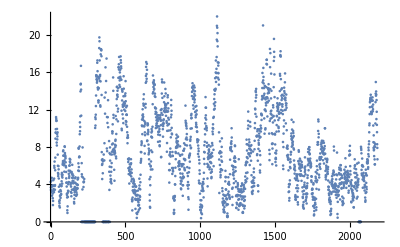

```mathematica
ListPlot[Table[{i,speedData[[i]]},{i,1,Length[speedData]}]]
```

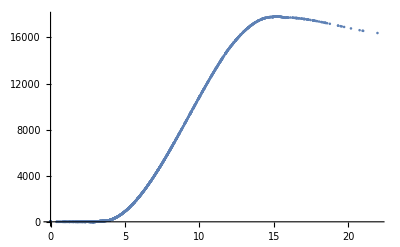

```mathematica
ListPlot[Table[{speedData[[i]],f[speedData[[i]]]},{i,1,Length[speedData]}]]
```

```mathematica
Plot[f[x],{x,speedData}]
```

Plot::pllim: Range specification {x,{4.28,3.68,3.42,3.4,3.2,3.93,4.42,4.71,3.28,2.8,3.8,3.92,3.82,3.02,2.53,1.8,2.24,3.87,4.46,3.51,3.38,3.88,3.18,4.63,5.99,5.78,6.45,3.84,3.44,3.93,5.52,6.87,8.9,9.56,9.91,9.51,11.2,11.01,10.79,10.83,8.48,8.17,9.94,9.4,8.82,9.14,9.57,7.19,6.,5.23,«2133»}} is not of the form {x, xmin, xmax}.

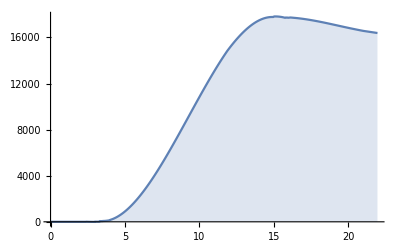

```mathematica
DiscretePlot[f[x],{x,speedData}]
```

```mathematica
predictedValues:=Map[f,speedData];
```

```mathematica
predictedValues[[3]]
```

59.5123

```mathematica
Plot[predictedValues]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[predictedValues]